# Projektuppgift 1

Course code: IX1500
Date: 2018-04-10

Erik Lenas, eriklen@kth.se
Melker Mossberg, melkermo@kth.se

Task 1: RSA cipher

## Summery

### Task

The task is to crack the given cipher encoded with RSA-cryptation. 
The numbers is the list seems to be of the same size. Why?

```mathematica
n=126456119090476383371855906671054993650778797793018127;
e=7937;
cipher={60833078379832053733665235104517667174744887177103669,47845135110330425759238983903835414959478333031403660,29226436027122547212719862444995325439654173683124719,26852073219160460393476539289841435348076003235573562,18536789208272843521201394019815486297145984481554371,60946204295190537657611153931568067486237180585452998,23651682987715782801807742133012602969829495021520007,112630050746349041975951827486336529408641182025699787,46387928110260904731968713144311859620686048715174256,101614383351383083936620333816943396668613455381224570};
```

### Result

The encrypted message is:

Congratulations! You have now managed to crack the RSA cipher. This means that you have a pass grade for project 2. If you want to pursue a higher grade you need to solve one more problem.

## Discussion

### Why does the numbers in the list seem to be of the same size?

The cipher is given as a list of equally long number because, for the RSA-encoding to work, M must satisfy 0≤M≤N-1since RSA works with modulo N. If M is bigger, we get a value from “next cycle of mod N”.

This means C = Mod[M^e,  n] will give the wrong value if M ≥ N.

### Our solution

We used FactorInteger[] to get “p” and “q” from the pubic key “n”. This is what makes very large value of n impossible to solve in reasonable time.

Then we took the multiplicative inverse of “e” to get “d”.

After decoding the given cipher, we converted all the decoded values into a String of ascii-letters.

## Code

```mathematica
ClearAll["`*"]
```

Decoding the cipher

```mathematica
list =FactorInteger[n];
p = 255471513878248459929909589;
q = 494991074232809803525292243;
ϕn = (p-1)(q-1); (* Calculating "phi of n" *)
d =PowerMod[e,-1,ϕn]; (* Calculating the multiplicative inverse of e *)
mFromAlice=PowerMod[cipher,d,n] (* Decoding cipher *)
```

Converting decoded values into String

```mathematica
B=256; (* Variable is used when converting from base 10 to base 256 *)
decodedList = {};
For[i=1,i<= Length[mFromAlice],i++, 
q=mFromAlice[[i]];ascii={};
While[q≠0,
AppendTo[ascii,Mod[q,B]];(* Every number in mFromAlice is converted to ascii*)
q=Quotient[q,B]
];
AppendTo[decodedList,FromCharacterCode[ascii]]; 
]
StringJoin[decodedList] (* All asci-letters are joined into String*)
```

Task 2: Combinatorial calculations

## Summery

### Task

Write a method RSAcrack[cipher,n,e] that will crack a standard RSA cipher and delivers clear text from the string cipher. When you are finished with your method, you should investigate how long it will take to crack the cipher of the English text “ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL.” for different sizes on your public key n (100-200 bits). Visualize your results in a proper graph. It is very important that you study the section 2.3 in the instructions. Your graph should lead you to a model where you can predict how long it would take to crack a cipher if n is 1024, 2048 bits or 4096 bits

Motivate your selected mathematical model!

### Result

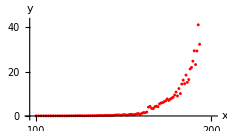
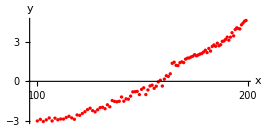
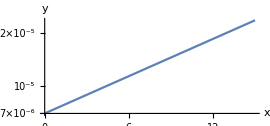
Graphs
Figure(1): This was the graph of execution-time of our RSA-crack for different “n”, where n range from 100 to 200, using linear data.
Figure(2): This graph uses logarithmic data for execution time. Here we can see that the graph can be approximated by a straight line.
Figure(3): Here we used FindFit[] to find a linear fit to the data used in Figure(2) to make predictions about large values for “n”.

  
-Graphics-      -Graphics-      -Graphics-
                   Figure(1)							         Figure(2)							            Figure(3)

Predictions
For n = 1024,		 Execution time = 9.466390912743541`   × 10^30  seconds 
For n = 2048,		 Execution time = 1.2839770091002624` × 10^67  seconds
For n = 4096,		 Execution time = 2.3621249819261243` × 10^139 seconds

## Discussion

### Motivate your selected mathematical model!

The data points in our plot (Figure(1)) seems to fit an exponential function, which is why we used FindFit[] with logarithmic values of execution time.

When making the predictions we see that RSA-encryption works very well since it would be practically impossible to decrypt with our method.

## Code

Create RSAcrack-function

```mathematica
ClearAll["`*"]
```

```mathematica
(* Takes encoded message, and keys n and e as argumenst*)
RSAcrack[cipher_,n_, e_]:=( 
list = FactorInteger[n];  (* Calculate p, q, e and d *)
p = list[[1,1]];
q = list[[2,1]];
ϕn = (p-1)(q-1);
d =PowerMod[e,-1,ϕn];
B=256;
decodedMessage=PowerMod[cipher,d,n]; (* Decode the cipher*)
message = {};
For[i=1,i<= Length[decodedMessage],i++, (* Convert decoded values to list of characters *)
q=decodedMessage[[i]];ascii={};
While[q≠0,
AppendTo[ascii,Mod[q,B]];
q=Quotient[q,B]
];
AppendTo[message,FromCharacterCode[ascii]];
];
StringJoin[message] (* Create a String from list*)
)
```

Encrypt message :  "ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."

```mathematica
(* Takes message to encryp, and bit size of n as arguments*)
RSAencrypt[messageToEncrypt_,bitSizeN_] := (
pqSize = Floor[bitSizeN/2]; (* Generate prime numbers p,q to create n of size bitSizeN *)
p2 = NextPrime[RandomInteger[{2^pqSize,2^(pqSize+1)}]];
q2 = NextPrime[RandomInteger[{2^pqSize,2^(pqSize+1)}]];
n2 = p2*q2; 
ϕn2=(p2-1)*(q2-1); (* Generate phi of n*)
rnd:=RandomInteger[{10^3,10^4}];
While[GCD[e2=rnd,ϕn2]≠1]; (* Generate e which is relative prime of phi of n *)

(* Start to encrypt our message *)
B = 256;
cipherList = {};
(* Split messageToEncrypt into 8 char long chunks, encrypt these and add to list *)
encryptedPackage = {};
For[i = 1, i < StringLength[messageToEncrypt], i=i+8,
splitMessage= StringPart[messageToEncrypt,i;;(i+7);;1];
joinedMessage = StringJoin[splitMessage];
message2=ToCharacterCode[joinedMessage]. B^(Range[StringLength[joinedMessage]]-1);
cipher2=PowerMod[message2,e2,n2];
AppendTo[cipherList,cipher2];
];
AppendTo[encryptedPackage, {n2,e2,cipherList}];
encryptedPackage
)
```

Test of encryption- and decryption function:

```mathematica
message = "ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL.";
encryptedPackage = RSAencrypt[message, 100];
n =encryptedPackage[[1,1]]; e = encryptedPackage[[1,2]]; cipherList = encryptedPackage[[1,3]];
RSAcrack[cipherList,n,e]
```

ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL.

Timing test : Tests execution times from BitLength[n] = 100 → 200 and saves the data  in list. Warning takes 20 minutes.

```mathematica
(* Save timeResult and nUsed for later use as Y and X values in graph *)
timeResult = {};nUsed = {};  
(* Run RSA-encrypt and RSA-crack with n-values from 100 to 200 *)
For[nSize = 100, nSize < 200, nSize++,
startTime = TimeUsed[];
encryptPackage = RSAencrypt[message,nSize];
n =encryptPackage[[1,1]]; e = encryptPackage[[1,2]]; cipherList = encryptPackage[[1,3]];
RSAcrack[cipherList, n,e];
endTime = TimeUsed[];
totalTime = endTime - startTime;
AppendTo[nUsed, nSize];
AppendTo[timeResult, totalTime]
]
timeResult;
nUsed;
```

Plot the data on graph

```mathematica
data=Transpose[{nUsed,Log[timeResult]}];
data0=Transpose[{nUsed,timeResult}];
dataplot=ListLogLinearPlot[data,AxesLabel->{x,y},PlotStyle->Red]
dataplot=ListLogLinearPlot[data0,AxesLabel->{x,y},PlotStyle->Red]
solution=FindFit[data,a x+b,{a,b},x];
y[x_]=ⅇ^(a x+b)/.solution;
modelplot=LogPlot[y[x],{x,0,15},AxesLabel->{x,y}];
Show[modelplot,dataplot]
```